```mathematica
(*Piosenka*)
(*Testowa piosenka*)
```

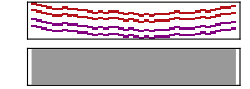

```mathematica
n=40;
T[x_]:=x+RandomChoice[{-1,0,1}];t=NestList[T,0,n];
a1=Table[SoundNote[{t[[k]],5+t[[k]]},{k,k+1},"Piano",SoundVolume->Sin[k/3]],{k,n}];
a2=Table[SoundNote[{12+t[[k]],17+t[[k]]},{k,k+1},"Flute",SoundVolume->Sin[k/2]],{k,n}];
Sound[Union[a1,a2],{0,6}]
```

```mathematica
(*Piosenka See you again*)
```

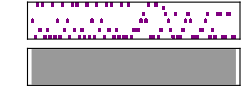

-Graphics-

```mathematica
Sound[{SoundNote["F",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["D",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["F",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["D",0.5],SoundNote["F",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["D",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["F",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["D",0.5],SoundNote["F",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["D",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["D",0.5],SoundNote["D",0.5],SoundNote["F",0.5],SoundNote["G",0.5],SoundNote["F",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["C",0.5],SoundNote["A#",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["A",0.5],SoundNote["G",0.5],SoundNote["F",0.5],SoundNote["D",0.5],SoundNote["C",0.5],SoundNote["G",0.5],SoundNote["C",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["F",0.5],SoundNote["G",0.5],SoundNote["F",0.5],SoundNote["C",0.5],SoundNote["C",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["D",0.5],SoundNote["F",0.5],SoundNote["G",0.5],SoundNote["C",0.5],SoundNote["D",0.5],SoundNote["C",0.5],SoundNote["G",0.5],SoundNote["G",0.5],SoundNote["C",0.5],SoundNote["C",0.5],SoundNote["G",0.5],SoundNote["G",0.5],SoundNote["C",0.5],SoundNote["C",0.5]}]
Play[Sin[2t^2],{t,0,5}]
```

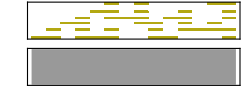

```mathematica
Sound[SoundNote[#,1/6,"Warm"]&/@(Pick[{0,5,9,12,16,21},#,1]&/@CellularAutomaton[30,{{1,0,0,0,0,0},0},13,{13,5}])]
```

```mathematica
(*Ustawianie*)
Manipulate[
DynamicModule[{rr},
rr=Flatten@Table[{a,b,c,d,e,f,g,h},{3}];
Sound[Flatten[#,1]&@{SoundNote[#,.25,"Percussion"]&/@RandomInteger[x,y],
MapIndexed[
SoundNote[#1,Flatten@{#2,#2+First@rr[[#2]]},Instruments]&,{d1,d2,d3,d4,d5,d6,d7,d8}],
MapIndexed[
SoundNote[#1,Flatten@{#2,#2+First@rr[[#2]]},Instruments2]&,{e1,e2,e3,e4,e5,e6,e7,e8}]}]],
Column[{
Row[{"sequence 1 notes ",PopupMenu[Dynamic[d1],{0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d2],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d3],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d4],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d5],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d6],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d7],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[d8],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}]}],
Row[{"sequence 2 notes",
PopupMenu[Dynamic[e1],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e2],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e3],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e4],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e5],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e6],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e7],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}],PopupMenu[Dynamic[e8],{None->Dynamic[None/.n3],0->Dynamic[0/.n3],1->Dynamic[1/.n3],2->Dynamic[2/.n3],3->Dynamic[3/.n3],4->Dynamic[4/.n3],5->Dynamic[5/.n3],6->Dynamic[6/.n3],7->Dynamic[7/.n3],8->Dynamic[8/.n3],9->Dynamic[9/.n3],10->Dynamic[10/.n3],11->Dynamic[11/.n3],12->Dynamic[12/.n3]}]}],
Row[{Column[{
"",
Style["note lengths",Bold],
Control[{{a,1," 1st"},0,5,.125,Slider,ImageSize->Small}],
Control[{{b,1,"2nd"},0,5,.125,Slider,ImageSize->Small}],
Control[{{c,1," 3rd"},0,5,.125,Slider,ImageSize->Small}],
Control[{{d,1," 4th"},0,5,.125,Slider,ImageSize->Small}],
Control[{{e,1," 5th"},0,5,.125,Slider,ImageSize->Small}],
Control[{{f,1," 6th"},0,5,.125,Slider,ImageSize->Small}],
Control[{{g,1," 7th"},0,5,.125,Slider,ImageSize->Small}],
Control[{{h,1," 8th"},0,5,.125,Slider,ImageSize->Small}]
}],
Column[{
Control[{{x,1,"number of percussion sounds"},plist}],
Control[{{y,0,"number of percussion notes "},plist2}],Control[{{Instruments,"Piano","sequence 1 instrument"},instrumentlist,ImageSize->Small}],
Control[{{Instruments2,"Piano","sequence 2 instrument"},instrumentlist,ImageSize->Small}]},
Alignment->Left]
},"\t  ",FrameMargins->10]}],
{{n3,{None->"Rest",0->"C",1->"C#",2->"D",3->"D#",4->"E",5->"F",6->"F#",7->"G",8->"G#",9->"A",10->"A#",11->"B",12->"C"}},ControlType-> None},
ControlPlacement->Top,
Alignment->Center,
SaveDefinitions->True,
AutorunSequencing-> {1}]
```